## Office

```mathematica
Get["G:\\My Drive\\PhD Pisa\\Calculations, Data and Designs\\Wolfram Mathematica\\SuperDataAnalysis.m"]
```

## Home

```mathematica
Get["D:\\Libraries\\_Google Drive SNS\\PhD Pisa\\Calculations, Data and Designs\\Wolfram Mathematica\\SuperDataAnalysis.m"]
```

## Initialization

### Working directory

```mathematica
SetWorkingDirectory[]
```

Working directory set to: D:\Libraries\_Google Drive SNS\Work From Home folder\PhD Thesis LaTeX\images\EFE_IL\

### Dataset

```mathematica
datasetFile=FileNameJoin[{NotebookDirectory[],"Nb_DB_13_datasets.wl"}]
```

D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Nb DB\Nb DB 14\Nb_DB_13_datasets.wl

```mathematica
Get[datasetFile];
```

#### variables

```mathematica
IonicGatingIcVTemp;
IonicGatingIrVTemp;
IonicGatingIcVTempRepetitions;
```

### Take quarter functions

```mathematica
TakeFirstQuarter[list_]:=list[[1;;Floor[Length[list]/4]]]
TakeSecondQuarter[list_]:=list[[Floor[Length[list]/4]+1;;2*Floor[Length[list]/4]]]
TakeThirdQuarter[list_]:=list[[2*Floor[Length[list]/4]+1;;3*Floor[Length[list]/4]]]
TakeFourthQuarter[list_]:=list[[3*Floor[Length[list]/4]+1;;Length[list]]]
```

#### Tests / behavior

```mathematica
TakeFirstQuarter[Range[12]]
TakeSecondQuarter[Range[12]]
TakeThirdQuarter[Range[12]]
TakeFourthQuarter[Range[12]]
```

{1,2,3}

{4,5,6}

{7,8,9}

{10,11,12}

```mathematica
TakeFirstQuarter[Range[13]]
TakeSecondQuarter[Range[13]]
TakeThirdQuarter[Range[13]]
TakeFourthQuarter[Range[13]]
```

{1,2,3}

{4,5,6}

{7,8,9}

{10,11,12,13}

```mathematica
TakeFirstQuarter[Range[14]]
TakeSecondQuarter[Range[14]]
TakeThirdQuarter[Range[14]]
TakeFourthQuarter[Range[14]]
```

{1,2,3}

{4,5,6}

{7,8,9}

{10,11,12,13,14}

### Determining I_C and I_R

#### I_C up and down

```mathematica
Clear[ShowIcStandard,FindIcStandard];
ShowIcStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]]},
(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

ShowFindSlopeArray[listX,listY,threshold,1,-1]
]

FindIcStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]],meanTemperature},
(*Take the average temperature of every sweep, then duplicate the list since we take two quarters*)
meanTemperature = Map[Mean,S2Split[TakeColumn[4]]];
meanTemperature=Join[meanTemperature,meanTemperature];

(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

(*Combine the average temperature of the sweep with the corrosponding Ic*)
Transpose[{meanTemperature,FindSlopeArray[listX,listY,threshold,1,-1]}]
]
```

#### I_R up and down

```mathematica
Clear[ShowIrStandard,FindIrStandard];
ShowIrStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]]},
(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

ShowFindSlopeArray[listX,listY,threshold,1,-1]
]

FindIrStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]],meanTemperature,Ir},
(*Take the average temperature of every sweep, then duplicate the list since we take two quarters*)
meanTemperature = Map[Mean,S2Split[TakeColumn[4]]];
meanTemperature=Join[meanTemperature,meanTemperature];

(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

Ir = FindSlopeArray[listX,listY,threshold,1,-1];
(*Ir=Map[#-3*&,Ir];*)
(*Combine the average temperature of the sweep with the corrosponding Ic*)
Transpose[{meanTemperature,Ir}]
]
```

## Save data sets

```mathematica
Save[datasetFile,IonicGatingIcVTemp]
Save[datasetFile,IonicGatingIrVTemp]
Save[datasetFile,IonicGatingIcVTempRepetitions]
```

### Examples

```mathematica
(*IonicGatingIcVTemp=Dataset[{<|"Device"->"Nb DB 14 dev C","Measurement"->"m003","VGate"->1,"IcvTemp"->Transpose[{meanTemp,Ic}]|>}]*)
```

```mathematica
(*IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m003","VGate"->0,"IcvTemp"->Transpose[{temp,Ic}]|>,1]*)
```

## Measurements

### m003 V_Gate = 0 V

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m003

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 25

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.}

Column 1 is current bias
Column 4 is ‘Temperature’ (badly calibrated sensor)
Column 5 is voltage drop

s2 is 25 repetitions

#### Misc

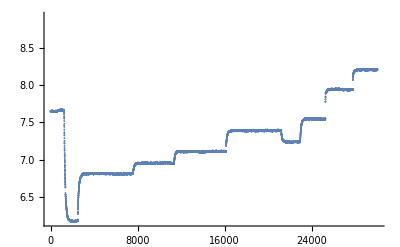

```mathematica
TakeColumn[4]//ListPlot
```

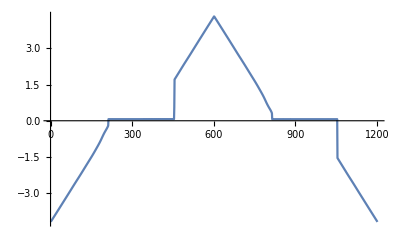

```mathematica
S2Split[TakeColumn[5]][[1]]//ListLinePlot
```

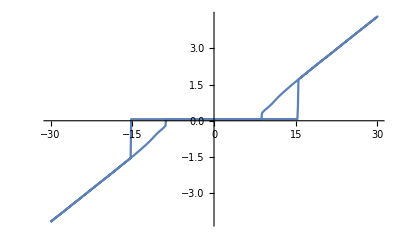

```mathematica
Transpose[{S2Split[TakeColumn[1]][[1]],S2Split[TakeColumn[5]][[1]]}]//ListLinePlot
```

```mathematica
S2Split[TakeColumn[1]][[1]]//Length
```

1202

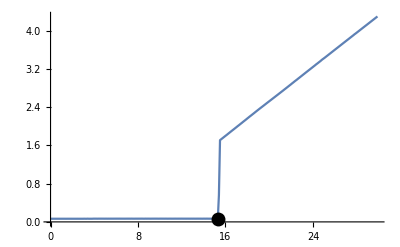
{154,15.3,-Graphics-}

```mathematica
Module[{listX =S2Split[TakeColumn[1]][[1]], listY =S2Split[TakeColumn[5]][[1]]},
ShowFindSlope[TakeSecondQuarter[listX],TakeSecondQuarter[listY],0.1]
]
```

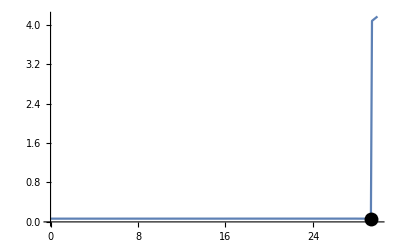
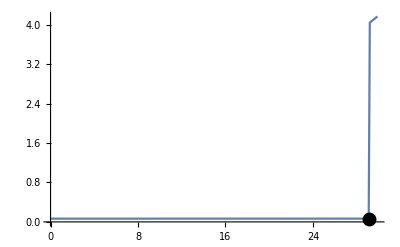
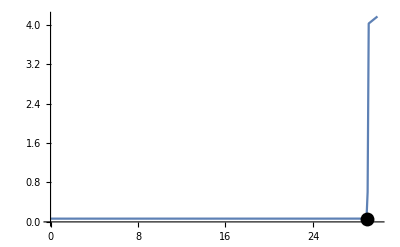
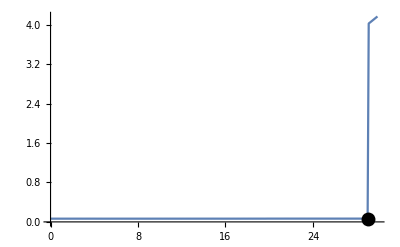
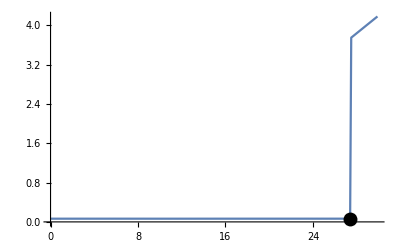
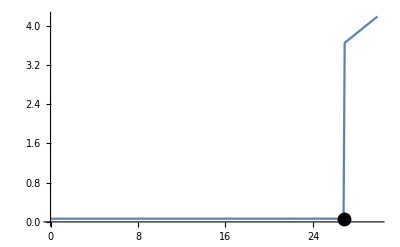
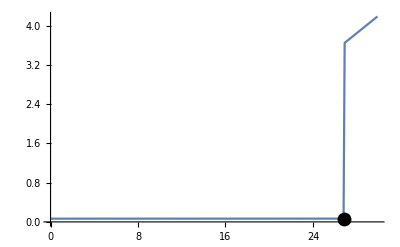
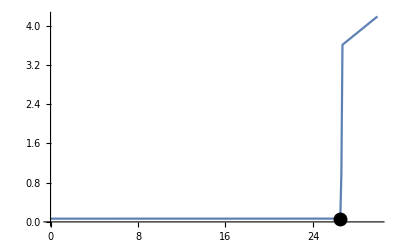
{{154,15.3,-Graphics-},{0,0,-Graphics-},{294,29.3,-Graphics-},{292,29.1,-Graphics-},{290,28.9,-Graphics-},{291,29.,-Graphics-},{275,27.4,-Graphics-},{269,26.8,-Graphics-},{269,26.8,-Graphics-},{266,26.5,-Graphics-},{242,24.1,-Graphics-},{242,24.1,-Graphics-},{242,24.1,-Graphics-},{235,23.4,-Graphics-},{196,19.5,-Graphics-},{197,19.6,-Graphics-},{196,19.5,-Graphics-},{197,19.6,-Graphics-},{222,22.1,-Graphics-},{175,17.4,-Graphics-},{173,17.2,-Graphics-},{112,11.1,-Graphics-},{110,10.9,-Graphics-},{77,7.6,-Graphics-},{72,7.1,-Graphics-}}

```mathematica
Module[{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},
listX = Map[TakeSecondQuarter,listX];
listY = Map[TakeSecondQuarter,listY];

ShowFindSlopeArray[listX,listY,0.1]
]
```

```mathematica
Module[{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},
listX = Map[TakeSecondQuarter,listX];
listY = Map[TakeSecondQuarter,listY];

FindSlopeArray[listX,listY,0.1]
]
```

{15.3,0,29.3,29.1,28.9,29.,27.4,26.8,26.8,26.5,24.1,24.1,24.1,23.4,19.5,19.6,19.5,19.6,22.1,17.4,17.2,11.1,10.9,7.6,7.1}

#### Temp

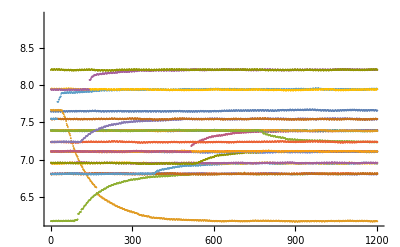

```mathematica
S2Split[TakeColumn[4]]//ListPlot
```

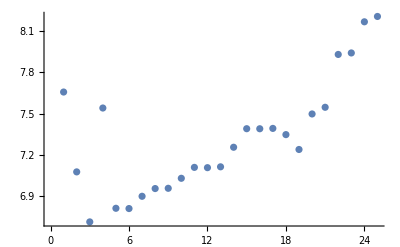

```mathematica
Map[Mean,S2Split[TakeColumn[4]]]//ListPlot
```

#### Removing data where T is unstable (manually)

```mathematica
S2Split[TakeColumn[4]]//ListPlot
```

-Graphics-

```mathematica
S2Split[TakeColumn[4]][[1]]//Max
S2Split[TakeColumn[4]][[1]]//Min
S2Split[TakeColumn[4]][[1]]//Mean
```

7.677

7.641

7.65649

```mathematica
Map[{Max[#],Min[#],Mean[#]}&,S2Split[TakeColumn[4]]]
```

{{7.677,7.641,7.65649},{873.,6.167,7.076},{6.82,6.174,6.71247},{880.,6.803,7.5403},{6.822,6.8,6.81142},{6.83,6.798,6.80952},{6.964,6.801,6.89865},{6.967,6.943,6.95487},{6.969,6.945,6.95674},{7.12,6.94,7.02946},{7.121,7.098,7.10881},{7.12,7.093,7.10671},{7.125,7.102,7.11285},{7.402,7.101,7.25508},{7.401,7.378,7.38994},{7.404,7.378,7.38958},{7.404,7.378,7.39209},{7.406,7.232,7.34694},{7.252,7.226,7.23884},{7.559,7.233,7.49709},{7.559,7.534,7.54562},{7.96,7.543,7.9297},{7.957,7.925,7.94058},{8.218,7.931,8.16702},{8.217,8.191,8.20584}}

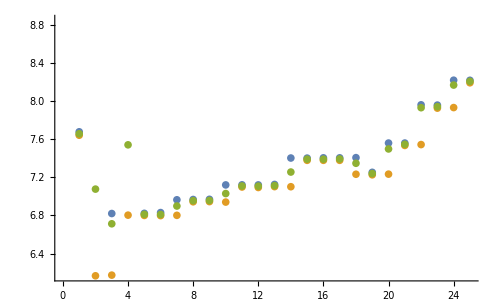

```mathematica
Module[{tData=Map[{Max[#],Min[#],Mean[#]}&,S2Split[TakeColumn[4]]]},
ListPlot[{Transpose[tData][[1]],Transpose[tData][[2]],Transpose[tData][[3]]}]
]
```

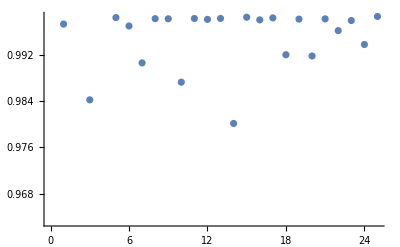

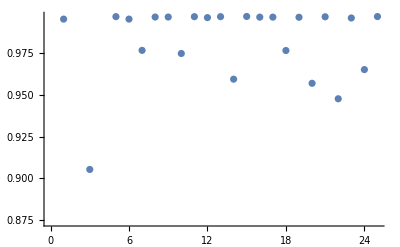

```mathematica
Module[{tData=Map[{Max[#],Min[#],Mean[#]}&,S2Split[TakeColumn[4]]]},
Map[#[[3]]/#[[1]]&,tData]//ListPlot//Print;
Map[#[[2]]/#[[1]]&,tData]//ListPlot //Print;
]
```

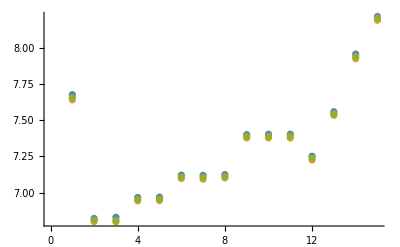

```mathematica
Module[{tData=Map[{Max[#],Min[#],Mean[#]}&,S2Split[TakeColumn[4]]]},

tData = Delete[tData,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

ListPlot[{Transpose[tData][[1]],Transpose[tData][[2]],Transpose[tData][[3]]}]
]
```

Second data set is unstable and has an erroneous point

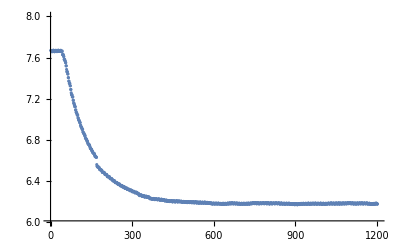

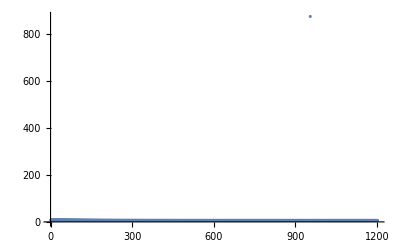

```mathematica
ListPlot[S2Split[TakeColumn[4]][[2]],PlotRange->{6,8}]
ListPlot[S2Split[TakeColumn[4]][[2]],PlotRange->Full]
```

#### Data second and fourth quarter (I_C unstable T data deleted)

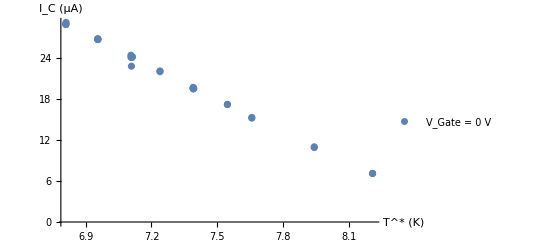

```mathematica
Module[{meanTemp, Ic,combined},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
(*Delete data with unstable T, then double the data as we want both up and down sweep Ic*)
meanTemp = Delete[meanTemp,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
meanTemp = Join[meanTemp,meanTemp];

Ic= Module[{listX, listY},
listX =S2Split[TakeColumn[1]];
listX = Delete[listX,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
 listY =S2Split[TakeColumn[5]];
listY = Delete[listY,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

FindSlopeArray[listX,listY,0.1]
];

combined = Transpose[{meanTemp,Ic}];

ListPlot[combined,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLegends->{"V_Gate = 0 V"}]
]
```

```mathematica
Module[{meanTemp, Ic,combined},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
(*Delete data with unstable T, then double the data as we want both up and down sweep Ic*)
meanTemp = Delete[meanTemp,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
meanTemp = Join[meanTemp,meanTemp];

Ic= Module[{listX, listY},
listX =S2Split[TakeColumn[1]];
listX = Delete[listX,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
 listY =S2Split[TakeColumn[5]];
listY = Delete[listY,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

FindSlopeArray[listX,listY,0.1]
];

combined = Transpose[{meanTemp,Ic}];

IonicGatingIcVTemp=Dataset[{<|"Device"->"Nb DB 14 dev C","Measurement"->"m003","VGate"->0,"IcvTemp"->combined|>}]
]
```

Dataset[<>]

#### Data first and third quarter (I_R unstable T data deleted)

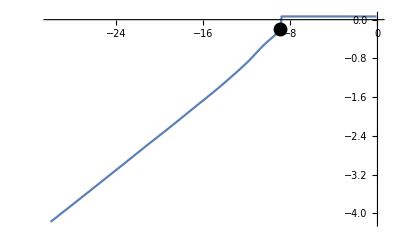
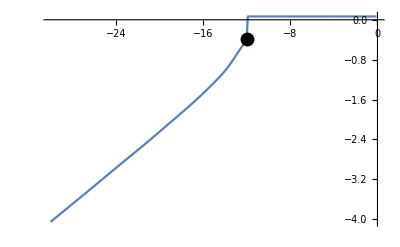
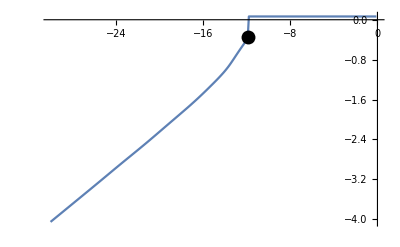
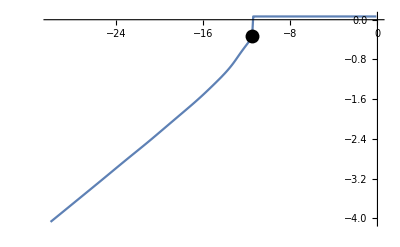
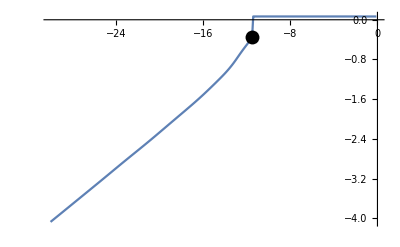
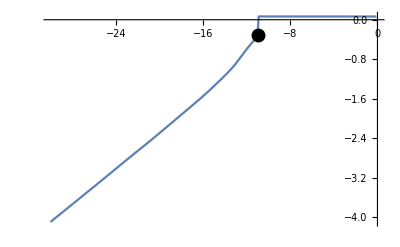
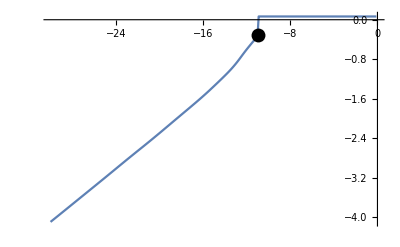
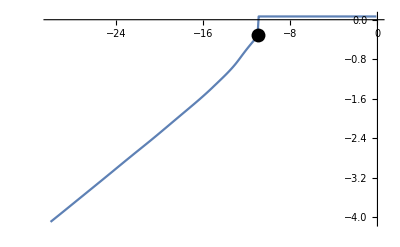
{{212,-8.9,-Graphics-},{181,-12.,-Graphics-},{182,-11.9,-Graphics-},{186,-11.5,-Graphics-},{186,-11.5,-Graphics-},{191,-11.,-Graphics-},{191,-11.,-Graphics-},{191,-11.,-Graphics-},{201,-10.,-Graphics-},{201,-10.,-Graphics-},{201,-10.,-Graphics-},{195,-10.6,-Graphics-},{208,-9.3,-Graphics-},{226,-7.5,-Graphics-},{241,-6.,-Graphics-},{86,8.7,-Graphics-},{117,11.8,-Graphics-},{118,11.9,-Graphics-},{113,11.4,-Graphics-},{113,11.4,-Graphics-},{108,10.9,-Graphics-},{108,10.9,-Graphics-},{108,10.9,-Graphics-},{98,9.9,-Graphics-},{98,9.9,-Graphics-},{98,9.9,-Graphics-},{103,10.4,-Graphics-},{91,9.2,-Graphics-},{73,7.4,-Graphics-},{58,5.9,-Graphics-}}

```mathematica
Module[{meanTemp, Ic,combined},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
(*Delete data with unstable T, then double the data as we want both up and down sweep Ic*)
meanTemp = Delete[meanTemp,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
meanTemp = Join[meanTemp,meanTemp];

Ic= Module[{listX, listY},
listX =S2Split[TakeColumn[1]];
listX = Delete[listX,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
 listY =S2Split[TakeColumn[5]];
listY = Delete[listY,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

listX = Join[Map[TakeFirstQuarter,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[TakeFirstQuarter,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

ShowFindSlopeArray[listX,listY,0.05]
]
]
```

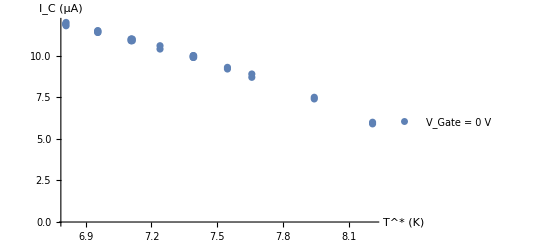

```mathematica
Module[{meanTemp, Ic,combined},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
(*Delete data with unstable T, then double the data as we want both up and down sweep Ic*)
meanTemp = Delete[meanTemp,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
meanTemp = Join[meanTemp,meanTemp];

Ic= Module[{listX, listY},
listX =S2Split[TakeColumn[1]];
listX = Delete[listX,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
 listY =S2Split[TakeColumn[5]];
listY = Delete[listY,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

listX = Join[Map[TakeFirstQuarter,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[TakeFirstQuarter,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

FindSlopeArray[listX,listY,0.05]
];

combined = Transpose[{meanTemp,Abs[Ic]}];

ListPlot[combined,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLegends->{"V_Gate = 0 V"}]
]
```

```mathematica
Module[{meanTemp, Ic,combined},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
(*Delete data with unstable T, then double the data as we want both up and down sweep Ic*)
meanTemp = Delete[meanTemp,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
meanTemp = Join[meanTemp,meanTemp];

Ic= Module[{listX, listY},
listX =S2Split[TakeColumn[1]];
listX = Delete[listX,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];
 listY =S2Split[TakeColumn[5]];
listY = Delete[listY,{{2},{3},{4},{7},{10},{14},{18},{20},{22},{24}}];

listX = Join[Map[TakeFirstQuarter,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[TakeFirstQuarter,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

FindSlopeArray[listX,listY,0.05]
];

combined = Transpose[{meanTemp,Abs[Ic]}];

IonicGatingIrVTemp=Dataset[{<|"Device"->"Nb DB 14 dev C","Measurement"->"m003","VGate"->0,"IrvTemp"->combined|>}]
]
```

Dataset[<>]

### m006 V_Gate= 1 V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m006

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

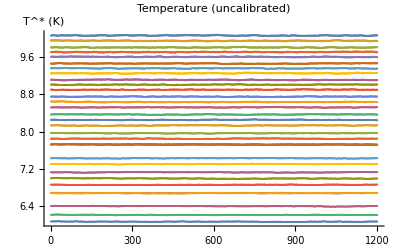

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

#### Show I_C

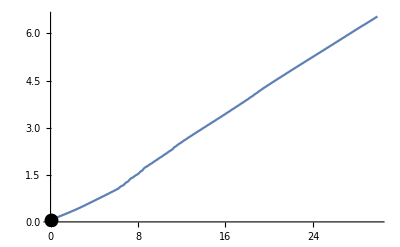
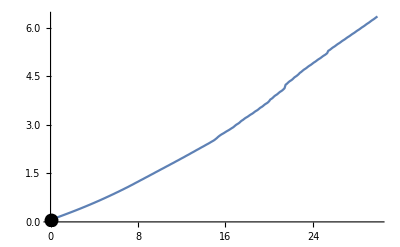
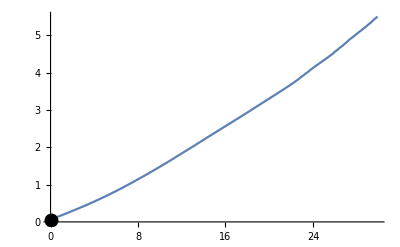
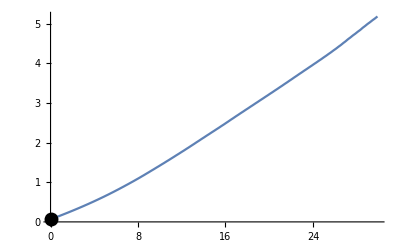
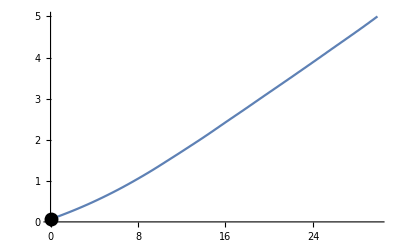
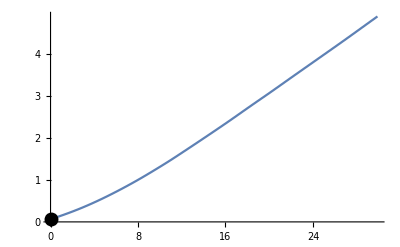
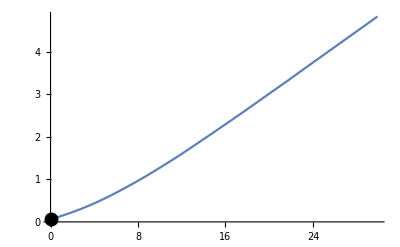
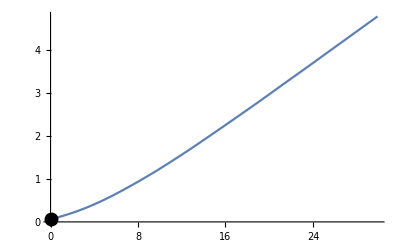
{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{7,0.6,-Graphics-},{13,1.2,-Graphics-},{23,2.2,-Graphics-},{33,3.2,-Graphics-},{43,4.2,-Graphics-},{56,5.5,-Graphics-},{68,6.7,-Graphics-},{84,8.3,-Graphics-},{105,10.4,-Graphics-},{112,11.1,-Graphics-},{143,14.2,-Graphics-},{122,12.1,-Graphics-},{171,17.,-Graphics-},{212,21.1,-Graphics-},{228,22.7,-Graphics-},{239,23.8,-Graphics-},{274,27.3,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{5,0.3,-Graphics-},{9,0.7,-Graphics-},{14,1.2,-Graphics-},{25,2.3,-Graphics-},{34,3.2,-Graphics-},{43,4.1,-Graphics-},{57,5.5,-Graphics-},{69,6.7,-Graphics-},{84,8.2,-Graphics-},{108,10.6,-Graphics-},{122,12.,-Graphics-},{136,13.4,-Graphics-},{126,12.4,-Graphics-},{192,19.,-Graphics-},{206,20.4,-Graphics-},{230,22.8,-Graphics-},{198,19.6,-Graphics-},{257,25.5,-Graphics-},{290,28.8,-Graphics-},{300,29.8,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

```mathematica
ShowIcStandard[]
```

#### Find I_C

```mathematica
FindIcStandard[]
```

{{10.0606,0.},{9.94761,0.},{9.8041,0.},{9.70592,0.},{9.6019,0.},{9.45981,0.},{9.35621,0.},{9.25166,0.},{9.10909,0.2},{9.00639,0.6},{8.89817,1.2},{8.7498,2.2},{8.63487,3.2},{8.51968,4.2},{8.36719,5.5},{8.2508,6.7},{8.1313,8.3},{7.96485,10.4},{7.84808,11.1},{7.72119,14.2},{7.72505,12.1},{7.42739,17.},{7.30262,21.1},{7.12649,22.7},{6.99429,23.8},{6.85862,27.3},{6.6818,-1},{6.67938,-1},{6.40075,-1},{6.21304,-1},{6.0688,-1},{10.0606,-0.1},{9.94761,-0.1},{9.8041,-0.1},{9.70592,-0.1},{9.6019,-0.1},{9.45981,-0.1},{9.35621,-0.1},{9.25166,-0.1},{9.10909,0.3},{9.00639,0.7},{8.89817,1.2},{8.7498,2.3},{8.63487,3.2},{8.51968,4.1},{8.36719,5.5},{8.2508,6.7},{8.1313,8.2},{7.96485,10.6},{7.84808,12.},{7.72119,13.4},{7.72505,12.4},{7.42739,19.},{7.30262,20.4},{7.12649,22.8},{6.99429,19.6},{6.85862,25.5},{6.6818,28.8},{6.67938,29.8},{6.40075,-1},{6.21304,-1},{6.0688,-1}}

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m006","VGate"->1,"IcvTemp"->FindIcStandard[]|>,1];
```

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{6,0.6,-Graphics-},{12,1.2,-Graphics-},{22,2.2,-Graphics-},{32,3.2,-Graphics-},{40,4.,-Graphics-},{49,4.9,-Graphics-},{57,5.7,-Graphics-},{64,6.4,-Graphics-},{73,7.3,-Graphics-},{79,7.9,-Graphics-},{85,8.5,-Graphics-},{85,8.5,-Graphics-},{98,9.8,-Graphics-},{103,10.3,-Graphics-},{109,10.9,-Graphics-},{114,11.4,-Graphics-},{118,11.8,-Graphics-},{123,12.3,-Graphics-},{123,12.3,-Graphics-},{130,13.,-Graphics-},{134,13.4,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{2,0.3,-Graphics-},{6,0.7,-Graphics-},{11,1.2,-Graphics-},{22,2.3,-Graphics-},{31,3.2,-Graphics-},{39,4.,-Graphics-},{49,5.,-Graphics-},{56,5.7,-Graphics-},{63,6.4,-Graphics-},{71,7.2,-Graphics-},{77,7.8,-Graphics-},{84,8.5,-Graphics-},{84,8.5,-Graphics-},{96,9.7,-Graphics-},{101,10.2,-Graphics-},{110,11.1,-Graphics-},{112,11.3,-Graphics-},{116,11.7,-Graphics-},{122,12.3,-Graphics-},{122,12.3,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]
```

{{10.0606,0.1},{9.94761,0.1},{9.8041,0.1},{9.70592,0.1},{9.6019,0.1},{9.45981,0.1},{9.35621,0.1},{9.25166,0.1},{9.10909,0.2},{9.00639,0.6},{8.89817,1.2},{8.7498,2.2},{8.63487,3.2},{8.51968,4.},{8.36719,4.9},{8.2508,5.7},{8.1313,6.4},{7.96485,7.3},{7.84808,7.9},{7.72119,8.5},{7.72505,8.5},{7.42739,9.8},{7.30262,10.3},{7.12649,10.9},{6.99429,11.4},{6.85862,11.8},{6.6818,12.3},{6.67938,12.3},{6.40075,13.},{6.21304,13.4},{6.0688,-1},{10.0606,0.2},{9.94761,0.2},{9.8041,0.2},{9.70592,0.2},{9.6019,0.2},{9.45981,0.2},{9.35621,0.2},{9.25166,0.2},{9.10909,0.3},{9.00639,0.7},{8.89817,1.2},{8.7498,2.3},{8.63487,3.2},{8.51968,4.},{8.36719,5.},{8.2508,5.7},{8.1313,6.4},{7.96485,7.2},{7.84808,7.8},{7.72119,8.5},{7.72505,8.5},{7.42739,9.7},{7.30262,10.2},{7.12649,11.1},{6.99429,11.3},{6.85862,11.7},{6.6818,12.3},{6.67938,12.3},{6.40075,-1},{6.21304,-1},{6.0688,-1}}

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m006","VGate"->1,"IrvTemp"->FindIrStandard[]|>,1];
```

### m009 V_Gate= 2V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m009

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 28

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3}

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{20,1.9,-Graphics-},{29,2.8,-Graphics-},{39,3.8,-Graphics-},{48,4.7,-Graphics-},{62,6.1,-Graphics-},{76,7.5,-Graphics-},{90,8.9,-Graphics-},{-1,-1,-Graphics-},{114,11.3,-Graphics-},{142,14.1,-Graphics-},{145,14.4,-Graphics-},{163,16.2,-Graphics-},{205,20.4,-Graphics-},{216,21.5,-Graphics-},{264,26.3,-Graphics-},{265,26.4,-Graphics-},{288,28.7,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{4,0.2,-Graphics-},{7,0.5,-Graphics-},{7,0.5,-Graphics-},{21,1.9,-Graphics-},{30,2.8,-Graphics-},{39,3.7,-Graphics-},{24,2.2,-Graphics-},{58,5.6,-Graphics-},{64,6.2,-Graphics-},{98,9.6,-Graphics-},{-1,-1,-Graphics-},{120,11.8,-Graphics-},{128,12.6,-Graphics-},{142,14.,-Graphics-},{163,16.1,-Graphics-},{176,17.4,-Graphics-},{220,21.8,-Graphics-},{242,24.,-Graphics-},{272,27.,-Graphics-},{291,28.9,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]
```

{{10.0233,0.},{9.92542,0.},{9.79511,0.},{9.69473,0.},{9.59524,0.},{9.45103,0.},{9.34859,0.},{9.24341,0.},{9.10977,0.2},{9.00091,0.5},{9.00495,0.5},{8.74759,1.9},{8.63819,2.8},{8.52341,3.8},{8.37394,4.7},{8.25684,6.1},{8.13502,7.5},{7.97504,8.9},{2.1852,-1},{7.72548,11.3},{7.55107,14.1},{7.42232,14.4},{7.2961,16.2},{7.1228,20.4},{6.98794,21.5},{6.85675,26.3},{6.6784,26.4},{6.54307,28.7},{10.0233,-0.1},{9.92542,-0.1},{9.79511,-0.1},{9.69473,-0.1},{9.59524,-0.1},{9.45103,-0.1},{9.34859,-0.1},{9.24341,-0.1},{9.10977,0.2},{9.00091,0.5},{9.00495,0.5},{8.74759,1.9},{8.63819,2.8},{8.52341,3.7},{8.37394,2.2},{8.25684,5.6},{8.13502,6.2},{7.97504,9.6},{2.1852,-1},{7.72548,11.8},{7.55107,12.6},{7.42232,14.},{7.2961,16.1},{7.1228,17.4},{6.98794,21.8},{6.85675,24.},{6.6784,27.},{6.54307,28.9}}

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m009","VGate"->2,"IcvTemp"->FindIcStandard[]|>,1];
```

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{5,0.5,-Graphics-},{5,0.5,-Graphics-},{20,2.,-Graphics-},{28,2.8,-Graphics-},{37,3.7,-Graphics-},{47,4.7,-Graphics-},{57,5.7,-Graphics-},{63,6.3,-Graphics-},{72,7.2,-Graphics-},{172,17.2,-Graphics-},{87,8.7,-Graphics-},{91,9.1,-Graphics-},{97,9.7,-Graphics-},{101,10.1,-Graphics-},{108,10.8,-Graphics-},{112,11.2,-Graphics-},{116,11.6,-Graphics-},{122,12.2,-Graphics-},{125,12.5,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{4,0.5,-Graphics-},{4,0.5,-Graphics-},{15,1.6,-Graphics-},{27,2.8,-Graphics-},{36,3.7,-Graphics-},{46,4.7,-Graphics-},{54,5.5,-Graphics-},{65,6.6,-Graphics-},{69,7.,-Graphics-},{-1,-1,-Graphics-},{82,8.3,-Graphics-},{90,9.1,-Graphics-},{96,9.7,-Graphics-},{100,10.1,-Graphics-},{107,10.8,-Graphics-},{111,11.2,-Graphics-},{115,11.6,-Graphics-},{120,12.1,-Graphics-},{124,12.5,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]
```

{{10.0233,0.1},{9.92542,0.1},{9.79511,0.1},{9.69473,0.1},{9.59524,0.1},{9.45103,0.1},{9.34859,0.1},{9.24341,0.1},{9.10977,0.2},{9.00091,0.5},{9.00495,0.5},{8.74759,2.},{8.63819,2.8},{8.52341,3.7},{8.37394,4.7},{8.25684,5.7},{8.13502,6.3},{7.97504,7.2},{2.1852,17.2},{7.72548,8.7},{7.55107,9.1},{7.42232,9.7},{7.2961,10.1},{7.1228,10.8},{6.98794,11.2},{6.85675,11.6},{6.6784,12.2},{6.54307,12.5},{10.0233,0.2},{9.92542,0.2},{9.79511,0.2},{9.69473,0.2},{9.59524,0.2},{9.45103,0.2},{9.34859,0.2},{9.24341,0.2},{9.10977,0.2},{9.00091,0.5},{9.00495,0.5},{8.74759,1.6},{8.63819,2.8},{8.52341,3.7},{8.37394,4.7},{8.25684,5.5},{8.13502,6.6},{7.97504,7.},{2.1852,-1},{7.72548,8.3},{7.55107,9.1},{7.42232,9.7},{7.2961,10.1},{7.1228,10.8},{6.98794,11.2},{6.85675,11.6},{6.6784,12.1},{6.54307,12.5}}

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m009","VGate"->2,"IrvTemp"->FindIrStandard[]|>,1];
```

### m012 V_Gate= 3V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m012

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 28

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3}

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

Bad curves: 23, 26, 56, even with increased threshold

#### Show I_C

```mathematica
ShowIcStandard[0.005]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{12,1.1,-Graphics-},{23,2.2,-Graphics-},{23,2.2,-Graphics-},{41,4.,-Graphics-},{54,5.3,-Graphics-},{65,6.4,-Graphics-},{69,6.8,-Graphics-},{76,7.5,-Graphics-},{104,10.3,-Graphics-},{113,11.2,-Graphics-},{136,13.5,-Graphics-},{152,15.1,-Graphics-},{3,0.2,-Graphics-},{206,20.5,-Graphics-},{213,21.2,-Graphics-},{16,1.5,-Graphics-},{-1,-1,-Graphics-},{289,28.8,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{7,0.5,-Graphics-},{14,1.2,-Graphics-},{24,2.2,-Graphics-},{24,2.2,-Graphics-},{42,4.,-Graphics-},{52,5.,-Graphics-},{58,5.6,-Graphics-},{71,6.9,-Graphics-},{73,7.1,-Graphics-},{106,10.4,-Graphics-},{92,9.,-Graphics-},{132,13.,-Graphics-},{152,15.,-Graphics-},{156,15.4,-Graphics-},{185,18.3,-Graphics-},{224,22.2,-Graphics-},{217,21.5,-Graphics-},{-1,-1,-Graphics-},{96,9.4,-Graphics-}}

#### Find I_C

Removing bad curves

```mathematica
FindIcStandard[]
```

{{10.031,0.},{9.9206,0.},{9.78702,0.},{9.79057,0.},{79.5074,0.},{86.9579,0.},{76.2684,0.},{63.0755,0.},{40.053,0.},{9.05428,0.1},{8.87978,1.1},{8.71257,2.1},{8.70898,2.2},{8.48727,4.},{8.3408,5.3},{8.22687,6.4},{8.11084,6.8},{8.11144,7.5},{7.83098,10.3},{7.70428,11.2},{7.53554,13.5},{7.40679,15.1},{7.2785,0.2},{7.1065,10.4},{6.97337,1.},{6.8385,0.5},{2.22936,-1},{6.52688,28.8},{10.031,-0.1},{9.9206,-0.1},{9.78702,-0.1},{9.79057,-0.1},{79.5074,-0.1},{86.9579,-0.1},{76.2684,-0.1},{63.0755,-0.1},{40.053,-0.1},{9.05428,0.4},{8.87978,1.1},{8.71257,2.1},{8.70898,2.2},{8.48727,4.},{8.3408,5.},{8.22687,5.6},{8.11084,6.9},{8.11144,7.1},{7.83098,10.4},{7.70428,9.},{7.53554,13.},{7.40679,15.},{7.2785,15.4},{7.1065,18.3},{6.97337,-0.1},{6.8385,0.3},{2.22936,-1},{6.52688,0.}}

```mathematica
ListPlot[FindIcStandard[0.005],PlotRange->{{0,10},{0,30}}]
ListPlot[Delete[FindIcStandard[0.005],{{23},{26},{56}}],PlotRange->{{0,10},{-1.5,30}}]
```

-Graphics-

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m012","VGate"->3,"IcvTemp"->Delete[FindIcStandard[0.005],{{23},{26},{56}}]|>,1];
```

#### Show I_R

Bad curves: 23, 26, 53, 54, 56

```mathematica
ShowIrStandard[0.005]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{11,1.1,-Graphics-},{22,2.2,-Graphics-},{22,2.2,-Graphics-},{39,3.9,-Graphics-},{48,4.8,-Graphics-},{55,5.5,-Graphics-},{63,6.3,-Graphics-},{65,6.5,-Graphics-},{82,8.2,-Graphics-},{84,8.4,-Graphics-},{93,9.3,-Graphics-},{97,9.7,-Graphics-},{1,0.1,-Graphics-},{110,11.,-Graphics-},{112,11.2,-Graphics-},{36,3.6,-Graphics-},{172,17.2,-Graphics-},{126,12.6,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{4,0.5,-Graphics-},{10,1.1,-Graphics-},{20,2.1,-Graphics-},{21,2.2,-Graphics-},{38,3.9,-Graphics-},{49,5.,-Graphics-},{54,5.5,-Graphics-},{65,6.6,-Graphics-},{64,6.5,-Graphics-},{76,7.7,-Graphics-},{83,8.4,-Graphics-},{90,9.1,-Graphics-},{97,9.8,-Graphics-},{101,10.2,-Graphics-},{107,10.8,-Graphics-},{10,1.1,-Graphics-},{85,8.6,-Graphics-},{-1,-1,-Graphics-},{3,0.4,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]
```

{{10.031,0.1},{9.9206,0.1},{9.78702,0.1},{9.79057,0.1},{79.5074,0.1},{86.9579,0.1},{76.2684,0.1},{63.0755,0.1},{40.053,0.1},{9.05428,0.1},{8.87978,1.1},{8.71257,2.1},{8.70898,2.2},{8.48727,3.9},{8.3408,4.8},{8.22687,5.5},{8.11084,6.3},{8.11144,6.5},{7.83098,8.2},{7.70428,8.4},{7.53554,9.3},{7.40679,9.7},{7.2785,0.1},{7.1065,2.8},{6.97337,0.7},{6.8385,1.4},{2.22936,17.2},{6.52688,12.6},{10.031,0.2},{9.9206,0.2},{9.78702,0.2},{9.79057,0.2},{79.5074,0.2},{86.9579,0.2},{76.2684,0.2},{63.0755,0.2},{40.053,0.2},{9.05428,0.4},{8.87978,1.1},{8.71257,2.1},{8.70898,2.2},{8.48727,3.9},{8.3408,5.},{8.22687,5.5},{8.11084,6.6},{8.11144,6.5},{7.83098,7.7},{7.70428,8.4},{7.53554,9.1},{7.40679,9.8},{7.2785,10.2},{7.1065,10.8},{6.97337,0.3},{6.8385,7.1},{2.22936,-1},{6.52688,0.4}}

```mathematica
ListPlot[FindIrStandard[0.005],PlotRange->{{0,10},{0,30}}]
ListPlot[Delete[FindIrStandard[0.005],{{23},{26},{53},{54},{56}}],PlotRange->{{0,10},{-1.5,30}}]
```

-Graphics-

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m012","VGate"->3,"IrvTemp"->Delete[FindIrStandard[0.005],{{23},{26},{53},{54},{56}}]|>,1];
```

### m017 V_Gate= 4V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m017

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{2,0.1,-Graphics-},{5,0.4,-Graphics-},{10,0.9,-Graphics-},{19,1.8,-Graphics-},{27,2.6,-Graphics-},{27,2.6,-Graphics-},{27,2.6,-Graphics-},{56,5.5,-Graphics-},{62,6.1,-Graphics-},{70,6.9,-Graphics-},{88,8.7,-Graphics-},{90,8.9,-Graphics-},{97,9.6,-Graphics-},{98,9.7,-Graphics-},{103,10.2,-Graphics-},{139,13.8,-Graphics-},{133,13.2,-Graphics-},{159,15.8,-Graphics-},{149,14.8,-Graphics-},{191,19.,-Graphics-},{180,17.9,-Graphics-},{232,23.1,-Graphics-},{224,22.3,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{3,0.1,-Graphics-},{6,0.4,-Graphics-},{11,0.9,-Graphics-},{20,1.8,-Graphics-},{28,2.6,-Graphics-},{28,2.6,-Graphics-},{27,2.5,-Graphics-},{55,5.3,-Graphics-},{65,6.3,-Graphics-},{72,7.,-Graphics-},{83,8.1,-Graphics-},{86,8.4,-Graphics-},{113,11.1,-Graphics-},{107,10.5,-Graphics-},{104,10.2,-Graphics-},{120,11.8,-Graphics-},{131,12.9,-Graphics-},{134,13.2,-Graphics-},{190,18.8,-Graphics-},{186,18.4,-Graphics-},{192,19.,-Graphics-},{218,21.6,-Graphics-},{232,23.,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m017","VGate"->4,"IcvTemp"->FindIcStandard[]|>,1];
```

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{4,0.4,-Graphics-},{9,0.9,-Graphics-},{18,1.8,-Graphics-},{26,2.6,-Graphics-},{26,2.6,-Graphics-},{26,2.6,-Graphics-},{52,5.2,-Graphics-},{60,6.,-Graphics-},{70,7.,-Graphics-},{76,7.6,-Graphics-},{87,8.7,-Graphics-},{89,8.9,-Graphics-},{99,9.9,-Graphics-},{104,10.4,-Graphics-},{106,10.6,-Graphics-},{116,11.6,-Graphics-},{120,12.,-Graphics-},{129,12.9,-Graphics-},{136,13.6,-Graphics-},{138,13.8,-Graphics-},{139,13.9,-Graphics-},{140,14.,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{3,0.4,-Graphics-},{8,0.9,-Graphics-},{17,1.8,-Graphics-},{25,2.6,-Graphics-},{25,2.6,-Graphics-},{24,2.5,-Graphics-},{53,5.4,-Graphics-},{58,5.9,-Graphics-},{68,6.9,-Graphics-},{77,7.8,-Graphics-},{89,9.,-Graphics-},{89,9.,-Graphics-},{94,9.5,-Graphics-},{101,10.2,-Graphics-},{109,11.,-Graphics-},{120,12.1,-Graphics-},{119,12.,-Graphics-},{129,13.,-Graphics-},{132,13.3,-Graphics-},{132,13.3,-Graphics-},{136,13.7,-Graphics-},{139,14.,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m017","VGate"->4,"IrvTemp"->FindIrStandard[]|>,1];
```

#### Switching instability

```mathematica
$s1Length
```

1202

```mathematica
ListLinePlot[Transpose[{S2Split[TakeColumn[1]][[18]],S2Split[TakeColumn[5]][[18]]}][[$s1Length/2;;$s1Length]],Mesh->Full,PlotRange->{{-10,10},{-1,1}}]
```

-Graphics-

```mathematica
ListLinePlot[TakeSecondQuarter[S2Split[TakeColumn[5]][[18]]],PlotRange->{{60,100},{0,1}},Mesh->Full]
```

-Graphics-

### m018 V_Gate= 4V, normal, 30 repetitions

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m018

First row of selectedFile: {s1,s2,s3,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 3

s1Length = 301

s2Length = 30

s3Length = 16

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.}

```mathematica
ListPlot[S3Split[TakeColumn[5]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### One set

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]][[4]], listY =S3S2Split[TakeColumn[6]][[4]]},

ShowFindSlopeArray[listX,listY,0.001]
]
```

{{123,12.2,-Graphics-},{126,12.5,-Graphics-},{134,13.3,-Graphics-},{119,11.8,-Graphics-},{122,12.1,-Graphics-},{122,12.1,-Graphics-},{126,12.5,-Graphics-},{161,16.,-Graphics-},{115,11.4,-Graphics-},{116,11.5,-Graphics-},{116,11.5,-Graphics-},{115,11.4,-Graphics-},{118,11.7,-Graphics-},{117,11.6,-Graphics-},{114,11.3,-Graphics-},{117,11.6,-Graphics-},{113,11.2,-Graphics-},{113,11.2,-Graphics-},{122,12.1,-Graphics-},{113,11.2,-Graphics-},{123,12.2,-Graphics-},{116,11.5,-Graphics-},{115,11.4,-Graphics-},{116,11.5,-Graphics-},{123,12.2,-Graphics-},{117,11.6,-Graphics-},{122,12.1,-Graphics-},{114,11.3,-Graphics-},{120,11.9,-Graphics-},{113,11.2,-Graphics-}}

```mathematica
Module[{meanTemp, Ic},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
Ic= Module[
{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},
listX = Map[TakeSecondQuarter,listX];
listY = Map[TakeSecondQuarter,listY];

FindSlopeArray[listX,listY,0.001]
];

ListPlot[Transpose[{meanTemp,Ic}],AxesLabel->{"T^* (K)","I_C (µA)"},PlotLegends->{"V_Gate = 1 V"}]
]
```

-Graphics-

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]][[5]], listY =S3S2Split[TakeColumn[6]][[5]]},
listX = Map[TakeSecondQuarter,listX];
listY = Map[TakeSecondQuarter,listY];

ShowFindSlopeArray[listX,listY,0.001]
]
```

#### All sets

```mathematica
Map[Mean,S3S2Split[TakeColumn[5]][[1]]]
```

{2.11715,2.1142,2.11158,2.10688,2.10691,2.10819,2.10823,2.11324,2.11306,2.11088,2.11523,2.11663,2.11255,2.11655,2.11576,2.11372,2.1117,2.11672,2.11731,2.11633,2.11356,2.11597,2.11838,2.1148,2.11807,2.12053,2.11384,2.11746,2.11763,2.11876}

```mathematica
Map[Mean,S3S2Split[TakeColumn[5]],2]
```

{2.11439,6.40043,2.22714,6.98666,7.29127,7.54895,7.84432,8.1307,8.38151,8.65482,8.90954,9.12198,9.37855,9.62508,9.83935,10.095}

```mathematica
Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]]
```

{{2.11715,2.1142,2.11158,2.10688,2.10691,2.10819,2.10823,2.11324,2.11306,2.11088,2.11523,2.11663,2.11255,2.11655,2.11576,2.11372,2.1117,2.11672,2.11731,2.11633,2.11356,2.11597,2.11838,2.1148,2.11807,2.12053,2.11384,2.11746,2.11763,2.11876},{6.39549,6.39923,6.40108,6.39545,6.39823,6.39849,6.40022,6.40102,6.39957,6.39822,6.39999,6.40103,6.40032,6.39889,6.39859,6.40069,6.39906,6.40362,6.40425,6.39914,6.40448,6.40451,6.40845,6.4068,6.40382,6.40039,6.4009,6.40231,6.39587,6.39264},{2.24438,2.2285,2.23009,2.22587,2.2282,2.22974,2.2258,2.22802,2.2263,2.22525,2.22649,2.22277,2.22523,2.22711,2.22637,2.22613,2.22641,2.22521,2.22557,2.22392,2.22654,2.22677,2.22716,2.22767,2.22624,2.22852,2.22979,2.22574,2.22384,2.22467},{6.98993,6.99022,6.98803,6.9912,6.98884,6.98665,6.98705,6.98847,6.98817,6.98747,6.98647,6.9859,6.98159,6.98465,6.98828,6.98695,6.98633,6.98631,6.98464,6.98761,6.98609,6.98593,6.98289,6.98713,6.98557,6.98851,6.9871,6.98235,6.98476,6.98465},{7.29466,7.29632,7.29633,7.295,7.29042,7.2925,7.29045,7.29474,7.29264,7.292,7.29387,7.29487,7.29137,7.28866,7.28974,7.29473,7.29333,7.28991,7.28815,7.29109,7.28833,7.28772,7.28601,7.2887,7.28764,7.2884,7.28944,7.2907,7.28935,7.29105},{7.54643,7.5477,7.54304,7.5448,7.54708,7.54838,7.54746,7.54789,7.55075,7.55165,7.54838,7.54612,7.549,7.55018,7.54721,7.54868,7.54862,7.55017,7.55136,7.55175,7.54908,7.54664,7.55216,7.54739,7.55279,7.55225,7.54996,7.55262,7.54916,7.54977},{7.84884,7.84369,7.84452,7.84513,7.84418,7.84414,7.84818,7.84103,7.84077,7.84242,7.83988,7.84373,7.84537,7.84452,7.84666,7.84835,7.84249,7.84336,7.8462,7.84662,7.8447,7.84235,7.84223,7.84753,7.84462,7.84457,7.84361,7.84349,7.84443,7.84199},{8.12925,8.13182,8.13037,8.13195,8.1268,8.12791,8.13086,8.13039,8.12904,8.1294,8.13081,8.12631,8.12977,8.12943,8.13384,8.1288,8.1321,8.13056,8.13037,8.13382,8.13485,8.13153,8.13147,8.13291,8.13336,8.13019,8.1287,8.12876,8.13106,8.13443},{8.36943,8.37111,8.37429,8.38279,8.37995,8.38353,8.38585,8.38592,8.38421,8.38287,8.38483,8.3844,8.37852,8.38121,8.38418,8.38056,8.38311,8.37912,8.37956,8.38156,8.38346,8.38478,8.38651,8.38053,8.3829,8.38372,8.37772,8.38017,8.38592,8.38267},{8.64968,8.65704,8.64944,8.65511,8.65563,8.65357,8.65651,8.6586,8.66066,8.65862,8.65503,8.65513,8.65404,8.6568,8.65448,8.65505,8.65211,8.66065,8.65715,8.65673,8.65185,8.65338,8.65013,8.65103,8.65543,8.65566,8.65124,8.65464,8.6542,8.65496},{8.91205,8.91219,8.91475,8.91315,8.90909,8.91641,8.91108,8.90873,8.91041,8.91292,8.90773,8.91004,8.90806,8.91108,8.90873,8.90951,8.90905,8.90975,8.90893,8.9103,8.91196,8.9075,8.9053,8.9031,8.90602,8.90483,8.90583,8.91087,8.90961,8.90716},{9.12532,9.12117,9.12515,9.11987,9.11819,9.11843,9.12504,9.12532,9.11873,9.12143,9.1233,9.12283,9.12113,9.12491,9.12145,9.12322,9.12013,9.12125,9.12554,9.12306,9.12405,9.12061,9.12006,9.12029,9.1251,9.12198,9.12404,9.11795,9.12064,9.11917},{9.38291,9.38402,9.382,9.38108,9.37675,9.38082,9.38147,9.38393,9.38177,9.38168,9.37651,9.38032,9.38006,9.38177,9.38077,9.38445,9.38006,9.3795,9.38188,9.37824,9.37802,9.37979,9.37518,9.37257,9.373,9.37092,9.37202,9.36937,9.37488,9.37079},{9.62668,9.62238,9.62488,9.61894,9.62298,9.62382,9.62375,9.61925,9.61962,9.6189,9.62184,9.62059,9.6185,9.62406,9.62832,9.63014,9.62784,9.62813,9.62634,9.62644,9.63122,9.63104,9.62791,9.62865,9.62582,9.62596,9.62518,9.6294,9.62682,9.62712},{9.84093,9.84442,9.83847,9.83736,9.84107,9.84278,9.84234,9.84005,9.83659,9.83762,9.83196,9.83382,9.83417,9.83559,9.83308,9.83425,9.82948,9.8331,9.83631,9.83365,9.83699,9.83737,9.83517,9.83703,9.84764,9.84964,9.85103,9.85022,9.85066,9.84759},{10.0967,10.0989,10.092,10.0897,10.0956,10.0958,10.094,10.0948,10.098,10.0939,10.0991,10.0987,10.0942,10.0998,10.0955,10.0973,10.096,10.0949,10.0973,10.0919,10.0947,10.0959,10.0961,10.0953,10.0943,10.0932,10.094,10.089,10.0893,10.0933}}

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];
ListPlot[Transpose[{temps,Ics}],PlotRange->{{6,10},{0,240}},ImageSize->Large,PlotLabel->"V_liquid = 4 V, 30 repititions",AxesLabel->{"T^* (K)","I_C (µA)"}]
]
```

-Graphics-

#### Dataset

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];
IonicGatingIcVTempRepetitions=Dataset[{<|"Device"->"Nb DB 14 dev C","Measurement"->"m018","VGate"->4,"IcvTemp"->Transpose[{temps,Ics}]|>}]
]
```

Dataset[<>]

### m019 V_Gate= 4V, normal, V source off (1 temperature)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2020-07-13 Nb DB\201030 
File name = m019

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 301

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.}

s2Length = 18

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.}

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

```mathematica
Module[{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},

ShowFindSlopeArray[listX,listY,0.001]
]
```

{{278,27.7,-Graphics-},{279,27.8,-Graphics-},{254,25.3,-Graphics-},{253,25.2,-Graphics-},{224,22.3,-Graphics-},{224,22.3,-Graphics-},{225,22.4,-Graphics-},{220,21.9,-Graphics-},{222,22.1,-Graphics-},{240,23.9,-Graphics-},{220,21.9,-Graphics-},{222,22.1,-Graphics-},{204,20.3,-Graphics-},{247,24.6,-Graphics-},{191,19.,-Graphics-},{205,20.4,-Graphics-},{203,20.2,-Graphics-},{214,21.3,-Graphics-}}

```mathematica
Module[{meanTemp, Ic},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
Ic= Module[
{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},
FindSlopeArray[listX,listY,0.001]
];

ListPlot[Transpose[{meanTemp,Ic}],AxesLabel->{"T^* (K)","I_C (µA)"},PlotLegends->{"V_Gate = 1 V"}]
]
```

-Graphics-

```mathematica
Module[{meanTemp, Ic},
meanTemp = Map[Mean,S2Split[TakeColumn[4]]];
Ic= Module[
{listX =S2Split[TakeColumn[1]], listY =S2Split[TakeColumn[5]]},
FindSlopeArray[listX,listY,0.001]
];

Mean[Ic]
]
```

22.8167

#### -> mean I_C = 228 µA at 6.65* K

### m021 V_Gate= 0V again, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m021

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

Bad curve: 22

```mathematica
ShowIcStandard[0.001]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{-1,-1,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{6,0.5,-Graphics-},{11,1.,-Graphics-},{20,1.9,-Graphics-},{30,2.9,-Graphics-},{39,3.8,-Graphics-},{49,4.8,-Graphics-},{56,5.5,-Graphics-},{66,6.5,-Graphics-},{72,7.1,-Graphics-},{79,7.8,-Graphics-},{87,8.6,-Graphics-},{94,9.3,-Graphics-},{37,3.6,-Graphics-},{106,10.5,-Graphics-},{113,11.2,-Graphics-},{114,11.3,-Graphics-},{131,13.,-Graphics-},{132,13.1,-Graphics-},{163,16.2,-Graphics-},{139,13.8,-Graphics-},{212,21.1,-Graphics-},{244,24.3,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{4,0.2,-Graphics-},{6,0.4,-Graphics-},{11,0.9,-Graphics-},{21,1.9,-Graphics-},{32,3.,-Graphics-},{40,3.8,-Graphics-},{50,4.8,-Graphics-},{59,5.7,-Graphics-},{65,6.3,-Graphics-},{75,7.3,-Graphics-},{82,8.,-Graphics-},{89,8.7,-Graphics-},{94,9.2,-Graphics-},{101,9.9,-Graphics-},{105,10.3,-Graphics-},{111,10.9,-Graphics-},{127,12.5,-Graphics-},{123,12.1,-Graphics-},{143,14.1,-Graphics-},{174,17.2,-Graphics-},{169,16.7,-Graphics-},{192,19.,-Graphics-},{234,23.2,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
Delete[FindIcStandard[],22]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m021","VGate"->0,"IcvTemp"->Delete[FindIcStandard[],22]|>,1]
```

Dataset[<>]

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{178,17.8,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{5,0.5,-Graphics-},{10,1.,-Graphics-},{19,1.9,-Graphics-},{29,2.9,-Graphics-},{38,3.8,-Graphics-},{47,4.7,-Graphics-},{56,5.6,-Graphics-},{61,6.1,-Graphics-},{75,7.5,-Graphics-},{82,8.2,-Graphics-},{85,8.5,-Graphics-},{92,9.2,-Graphics-},{109,10.9,-Graphics-},{103,10.3,-Graphics-},{113,11.3,-Graphics-},{115,11.5,-Graphics-},{117,11.7,-Graphics-},{131,13.1,-Graphics-},{137,13.7,-Graphics-},{136,13.6,-Graphics-},{140,14.,-Graphics-},{145,14.5,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{4,0.5,-Graphics-},{8,0.9,-Graphics-},{18,1.9,-Graphics-},{28,2.9,-Graphics-},{37,3.8,-Graphics-},{47,4.8,-Graphics-},{53,5.4,-Graphics-},{61,6.2,-Graphics-},{71,7.2,-Graphics-},{76,7.7,-Graphics-},{84,8.5,-Graphics-},{92,9.3,-Graphics-},{96,9.7,-Graphics-},{105,10.6,-Graphics-},{114,11.5,-Graphics-},{116,11.7,-Graphics-},{116,11.7,-Graphics-},{130,13.1,-Graphics-},{136,13.7,-Graphics-},{134,13.5,-Graphics-},{144,14.5,-Graphics-},{138,13.9,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m021","VGate"->0,"IrvTemp"->FindIrStandard[]|>,1]
```

Dataset[<>]

### m024 V_Gate= -1V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m024

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{6,0.5,-Graphics-},{11,1.,-Graphics-},{21,2.,-Graphics-},{29,2.8,-Graphics-},{39,3.8,-Graphics-},{52,5.1,-Graphics-},{63,6.2,-Graphics-},{74,7.3,-Graphics-},{98,9.7,-Graphics-},{116,11.5,-Graphics-},{133,13.2,-Graphics-},{162,16.1,-Graphics-},{180,17.9,-Graphics-},{168,16.7,-Graphics-},{186,18.5,-Graphics-},{222,22.1,-Graphics-},{225,22.4,-Graphics-},{287,28.6,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{4,0.2,-Graphics-},{7,0.5,-Graphics-},{12,1.,-Graphics-},{21,1.9,-Graphics-},{30,2.8,-Graphics-},{40,3.8,-Graphics-},{53,5.1,-Graphics-},{67,6.5,-Graphics-},{77,7.5,-Graphics-},{96,9.4,-Graphics-},{118,11.6,-Graphics-},{135,13.3,-Graphics-},{162,16.,-Graphics-},{154,15.2,-Graphics-},{179,17.7,-Graphics-},{198,19.6,-Graphics-},{218,21.6,-Graphics-},{218,21.6,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m024","VGate"->-1,"IcvTemp"->FindIcStandard[]|>,1]
```

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{5,0.5,-Graphics-},{10,1.,-Graphics-},{19,1.9,-Graphics-},{27,2.7,-Graphics-},{37,3.7,-Graphics-},{47,4.7,-Graphics-},{54,5.4,-Graphics-},{60,6.,-Graphics-},{69,6.9,-Graphics-},{75,7.5,-Graphics-},{81,8.1,-Graphics-},{89,8.9,-Graphics-},{95,9.5,-Graphics-},{100,10.,-Graphics-},{107,10.7,-Graphics-},{113,11.3,-Graphics-},{115,11.5,-Graphics-},{121,12.1,-Graphics-},{124,12.4,-Graphics-},{128,12.8,-Graphics-},{132,13.2,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{4,0.5,-Graphics-},{9,1.,-Graphics-},{18,1.9,-Graphics-},{27,2.8,-Graphics-},{36,3.7,-Graphics-},{46,4.7,-Graphics-},{53,5.4,-Graphics-},{59,6.,-Graphics-},{68,6.9,-Graphics-},{74,7.5,-Graphics-},{80,8.1,-Graphics-},{88,8.9,-Graphics-},{94,9.5,-Graphics-},{99,10.,-Graphics-},{106,10.7,-Graphics-},{110,11.1,-Graphics-},{114,11.5,-Graphics-},{119,12.,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m024","VGate"->-1,"IrvTemp"->FindIrStandard[]|>,1]
```

Dataset[<>]

### m027 V_Gate= -2V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m027

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{2,0.1,-Graphics-},{5,0.4,-Graphics-},{11,1.,-Graphics-},{20,1.9,-Graphics-},{28,2.7,-Graphics-},{37,3.6,-Graphics-},{51,5.,-Graphics-},{62,6.1,-Graphics-},{75,7.4,-Graphics-},{98,9.7,-Graphics-},{115,11.4,-Graphics-},{132,13.1,-Graphics-},{153,15.2,-Graphics-},{175,17.4,-Graphics-},{173,17.2,-Graphics-},{222,22.1,-Graphics-},{237,23.6,-Graphics-},{271,27.,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{3,0.1,-Graphics-},{7,0.5,-Graphics-},{11,0.9,-Graphics-},{21,1.9,-Graphics-},{29,2.7,-Graphics-},{39,3.7,-Graphics-},{52,5.,-Graphics-},{64,6.2,-Graphics-},{80,7.8,-Graphics-},{99,9.7,-Graphics-},{116,11.4,-Graphics-},{137,13.5,-Graphics-},{161,15.9,-Graphics-},{181,17.9,-Graphics-},{179,17.7,-Graphics-},{189,18.7,-Graphics-},{248,24.6,-Graphics-},{272,27.,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m027","VGate"->-2,"IcvTemp"->FindIcStandard[]|>,1]
```

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{4,0.4,-Graphics-},{9,0.9,-Graphics-},{19,1.9,-Graphics-},{27,2.7,-Graphics-},{36,3.6,-Graphics-},{46,4.6,-Graphics-},{53,5.3,-Graphics-},{60,6.,-Graphics-},{69,6.9,-Graphics-},{76,7.6,-Graphics-},{82,8.2,-Graphics-},{89,8.9,-Graphics-},{95,9.5,-Graphics-},{95,9.5,-Graphics-},{106,10.6,-Graphics-},{111,11.1,-Graphics-},{115,11.5,-Graphics-},{120,12.,-Graphics-},{124,12.4,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{4,0.5,-Graphics-},{8,0.9,-Graphics-},{18,1.9,-Graphics-},{26,2.7,-Graphics-},{35,3.6,-Graphics-},{45,4.6,-Graphics-},{52,5.3,-Graphics-},{59,6.,-Graphics-},{69,7.,-Graphics-},{74,7.5,-Graphics-},{80,8.1,-Graphics-},{88,8.9,-Graphics-},{94,9.5,-Graphics-},{94,9.5,-Graphics-},{105,10.6,-Graphics-},{110,11.1,-Graphics-},{114,11.5,-Graphics-},{119,12.,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m027","VGate"->-2,"IrvTemp"->FindIrStandard[]|>,1]
```

Dataset[<>]

### m030 V_Gate= -3V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m030

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{5,0.4,-Graphics-},{9,0.8,-Graphics-},{16,1.5,-Graphics-},{26,2.5,-Graphics-},{35,3.4,-Graphics-},{45,4.4,-Graphics-},{60,5.9,-Graphics-},{73,7.2,-Graphics-},{90,8.9,-Graphics-},{113,11.2,-Graphics-},{122,12.1,-Graphics-},{133,13.2,-Graphics-},{178,17.7,-Graphics-},{197,19.6,-Graphics-},{219,21.8,-Graphics-},{248,24.7,-Graphics-},{250,24.9,-Graphics-},{293,29.2,-Graphics-},{-1,-1,-Graphics-},{287,28.6,-Graphics-},{277,27.6,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{5,0.3,-Graphics-},{10,0.8,-Graphics-},{16,1.4,-Graphics-},{27,2.5,-Graphics-},{36,3.4,-Graphics-},{46,4.4,-Graphics-},{61,5.9,-Graphics-},{69,6.7,-Graphics-},{90,8.8,-Graphics-},{97,9.5,-Graphics-},{129,12.7,-Graphics-},{151,14.9,-Graphics-},{178,17.6,-Graphics-},{169,16.7,-Graphics-},{220,21.8,-Graphics-},{249,24.7,-Graphics-},{163,16.1,-Graphics-},{293,29.1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{260,25.8,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m030","VGate"->-3,"IcvTemp"->FindIcStandard[]|>,1]
```

Dataset[<>]

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{3,0.3,-Graphics-},{8,0.8,-Graphics-},{14,1.4,-Graphics-},{25,2.5,-Graphics-},{34,3.4,-Graphics-},{42,4.2,-Graphics-},{52,5.2,-Graphics-},{59,5.9,-Graphics-},{66,6.6,-Graphics-},{74,7.4,-Graphics-},{81,8.1,-Graphics-},{87,8.7,-Graphics-},{94,9.4,-Graphics-},{100,10.,-Graphics-},{104,10.4,-Graphics-},{111,11.1,-Graphics-},{115,11.5,-Graphics-},{119,11.9,-Graphics-},{124,12.4,-Graphics-},{128,12.8,-Graphics-},{131,13.1,-Graphics-},{135,13.5,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{3,0.4,-Graphics-},{7,0.8,-Graphics-},{13,1.4,-Graphics-},{24,2.5,-Graphics-},{33,3.4,-Graphics-},{41,4.2,-Graphics-},{51,5.2,-Graphics-},{58,5.9,-Graphics-},{65,6.6,-Graphics-},{74,7.5,-Graphics-},{80,8.1,-Graphics-},{86,8.7,-Graphics-},{93,9.4,-Graphics-},{98,9.9,-Graphics-},{103,10.4,-Graphics-},{109,11.,-Graphics-},{114,11.5,-Graphics-},{118,11.9,-Graphics-},{-1,-1,-Graphics-},{127,12.8,-Graphics-},{130,13.1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m030","VGate"->-3,"IrvTemp"->FindIrStandard[]|>,1]
```

Dataset[<>]

### m033 V_Gate= -4V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m033

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### Show I_C

```mathematica
ShowIcStandard[]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{6,0.5,-Graphics-},{12,1.1,-Graphics-},{23,2.2,-Graphics-},{31,3.,-Graphics-},{41,4.,-Graphics-},{55,5.4,-Graphics-},{68,6.7,-Graphics-},{68,6.7,-Graphics-},{98,9.7,-Graphics-},{107,10.6,-Graphics-},{107,10.6,-Graphics-},{162,16.1,-Graphics-},{185,18.4,-Graphics-},{180,17.9,-Graphics-},{147,14.6,-Graphics-},{209,20.8,-Graphics-},{271,27.,-Graphics-},{275,27.4,-Graphics-},{208,20.7,-Graphics-},{250,24.9,-Graphics-},{-1,-1,-Graphics-},{295,29.4,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{4,0.2,-Graphics-},{7,0.5,-Graphics-},{13,1.1,-Graphics-},{23,2.1,-Graphics-},{32,3.,-Graphics-},{42,4.,-Graphics-},{56,5.4,-Graphics-},{68,6.6,-Graphics-},{60,5.8,-Graphics-},{97,9.5,-Graphics-},{111,10.9,-Graphics-},{141,13.9,-Graphics-},{98,9.6,-Graphics-},{189,18.7,-Graphics-},{210,20.8,-Graphics-},{161,15.9,-Graphics-},{261,25.9,-Graphics-},{272,27.,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

#### Find I_C

```mathematica
FindIcStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m033","VGate"->-4,"IcvTemp"->FindIcStandard[]|>,1]
```

Dataset[<>]

#### Show I_R

```mathematica
ShowIrStandard[]
```

{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{5,0.5,-Graphics-},{11,1.1,-Graphics-},{22,2.2,-Graphics-},{30,3.,-Graphics-},{38,3.8,-Graphics-},{49,4.9,-Graphics-},{56,5.6,-Graphics-},{55,5.5,-Graphics-},{71,7.1,-Graphics-},{77,7.7,-Graphics-},{84,8.4,-Graphics-},{91,9.1,-Graphics-},{96,9.6,-Graphics-},{101,10.1,-Graphics-},{108,10.8,-Graphics-},{112,11.2,-Graphics-},{116,11.6,-Graphics-},{122,12.2,-Graphics-},{125,12.5,-Graphics-},{129,12.9,-Graphics-},{133,13.3,-Graphics-},{136,13.6,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{5,0.6,-Graphics-},{10,1.1,-Graphics-},{20,2.1,-Graphics-},{29,3.,-Graphics-},{37,3.8,-Graphics-},{48,4.9,-Graphics-},{54,5.5,-Graphics-},{55,5.6,-Graphics-},{70,7.1,-Graphics-},{76,7.7,-Graphics-},{82,8.3,-Graphics-},{90,9.1,-Graphics-},{95,9.6,-Graphics-},{101,10.2,-Graphics-},{107,10.8,-Graphics-},{111,11.2,-Graphics-},{115,11.6,-Graphics-},{120,12.1,-Graphics-},{124,12.5,-Graphics-},{127,12.8,-Graphics-},{132,13.3,-Graphics-},{135,13.6,-Graphics-}}

#### Find I_R

```mathematica
FindIrStandard[]//ListPlot
```

-Graphics-

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m033","VGate"->-4,"IrvTemp"->FindIrStandard[]|>,1]
```

Dataset[<>]

### m034 V_Gate= -4V, normal, 30 repetitions V source off

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m034

First row of selectedFile: {s1,s2,s3,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 3

s1Length = 301

s2Length = 30

s3Length = 16

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.}

```mathematica
ListPlot[S3Split[TakeColumn[5]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### All sets

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];
ListPlot[Transpose[{temps,Ics}],PlotRange->{{6,10},{0,240}},ImageSize->Large,PlotLabel->"V_liquid = -4 V, 30 repititions",AxesLabel->{"T^* (K)","I_C (µA)"}]
]
```

-Graphics-

#### Dataset

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];

IonicGatingIcVTempRepetitions=Insert[IonicGatingIcVTempRepetitions,<|"Device"->"Nb DB 14 dev C","Measurement"->"m034","VGate"->-4,"IcvTemp"->Transpose[{temps,Ics}]|>,1]
]
```

Dataset[<>]

### m035 V_Gate= 3V, normal, 30 repetitions V source off

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m035

First row of selectedFile: {s1,s2,s3,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 3

s1Length = 301

s2Length = 30

s3Length = 31

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
ListPlot[S3Split[TakeColumn[5]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

-Graphics-

#### All sets

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];
ListPlot[Transpose[{temps,Ics}],PlotRange->{{6,10},{0,240}},ImageSize->Large,PlotLabel->"V_liquid = -4 V, 30 repititions",AxesLabel->{"T^* (K)","I_C (µA)"}]
]
```

-Graphics-

#### Dataset

```mathematica
Module[{listX =S3S2Split[TakeColumn[1]], listY =S3S2Split[TakeColumn[6]], temps = Map[Map[Mean,#]&,S3S2Split[TakeColumn[5]]],Ics},

Ics=MapThread[FindSlopeArray[#1,#2,0.001]&,{listX,listY}];
Ics = 10*Flatten[Ics];
temps = Flatten[temps];

IonicGatingIcVTempRepetitions=Insert[IonicGatingIcVTempRepetitions,<|"Device"->"Nb DB 14 dev C","Measurement"->"m035","VGate"->3,"IcvTemp"->Transpose[{temps,Ics}]|>,1]
]
```

Dataset[<>]

## Plots I_C

### All standard measurements

#### I_C

```mathematica
IonicGatingIcVTemp
```

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

#### I_R

```mathematica
IonicGatingIrVTemp
```

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIrVTemp[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IrvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

### I_C compared to I_R

```mathematica
IonicGatingIcVTemp[All,#Measurement&]
```

Dataset[<>]

#### m003 (0 V)

```mathematica
Module[{data, measurement="m003"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

#### m006 (1 V)

```mathematica
Module[{data, measurement="m006"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

#### m017 (4 V)

```mathematica
Module[{data, measurement="m017"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

### Repetitions

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIcVTempRepetitions[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{dataset, legend},
dataset = Drop[IonicGatingIcVTempRepetitions[SortBy[#Measurement&]],1];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},{0,350}},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

### I_C, I_R and Repetitions at 4 V

```mathematica
Module[{data, measurement="m017"},
data={
Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],
Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]],
Normal[IonicGatingIcVTempRepetitions[Select[#Measurement=="m018"&]][1,#IcvTemp&]]
};


ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R","I_C"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

### I_C at 1V, I_R and Repetitions at 4 V

```mathematica
Module[{data},
data={
Normal[IonicGatingIcVTemp[Select[#Measurement=="m006"&]][1,#IcvTemp&]],
Normal[IonicGatingIrVTemp[Select[#Measurement=="m017"&]][1,#IrvTemp&]],
Normal[IonicGatingIcVTempRepetitions[Select[#Measurement=="m018"&]][1,#IcvTemp&]]
};
ListPlot[data,PlotRange->{{6,9.5},{0,310}},PlotLegends->{"I_C","I_R","I_C"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{data},
data={
Normal[IonicGatingIrVTemp[Select[#Measurement=="m017"&]][1,#IrvTemp&]],
Normal[IonicGatingIcVTempRepetitions[Select[#Measurement=="m018"&]][1,#IcvTemp&]]
};
ListPlot[data,PlotRange->{{6,9.5},{0,310}},PlotLegends->{"I_C","I_R","I_C"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14, V_Liquid = 4 V ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

### I_C at 1V, I_R and Repetitions at 3 V

```mathematica
Module[{data},
data={
Normal[IonicGatingIcVTemp[Select[#Measurement=="m006"&]][1,#IcvTemp&]],
Normal[IonicGatingIrVTemp[Select[#Measurement=="m017"&]][1,#IrvTemp&]],
Normal[IonicGatingIcVTempRepetitions[Select[#Measurement=="m035"&]][1,#IcvTemp&]]
};
ListPlot[data,PlotRange->{{6,9.5},{0,310}},PlotLegends->{"I_C","I_R","I_C"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

## Bardeen’s fit

### Bardeen’s fit data prep

```mathematica
Module[{data, measurement="m003"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{data, dataset =IonicGatingIcVTemp },
data=IonicGatingIcVTemp[Select[#Measurement=="m003"||#Measurement == "m006"&]][SortBy[#Measurement&]];
data={
Normal[data[[1]][#IcvTemp&]],
Normal[data[[2]][#IcvTemp&]]
};

ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{data1,data2, dataset =IonicGatingIcVTemp },
data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];

data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

Join[data1,data2]//ListPlot
]
```

-Graphics-

### Bardeen’s function I_c fit

```mathematica
Clear[IcBardeen]
IcBardeen[IC0_,Tc_,T_]:=Re[IC0*(1-(T/Tc)^2)^(3/2)]
```

#### ref plot

```mathematica
fitBardeen=Module[{data1,data2,data, dataset =IonicGatingIcVTemp ,Tc=9.1},

data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

NonlinearModelFit[data,IcBardeen[Ic0,Tc,T],{Ic0},T]
]

Show[{
Module[{data1,data2,data, dataset =IonicGatingIcVTemp, Ir},
dataset = IVsDataset[Select[#VGate==VGate&]];

data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

Ir=Normal[IonicGatingIrVTemp[Select[#Measurement == "m006"&]][[1]][#IrvTemp&]];

ListPlot[{data,Ir},PlotRange->{{6,10},{0,350}},AxesLabel->{"T (K)","I_C (µA)"},PlotLabel->"Nb 14",ImageSize->Large,PlotMarkers->{Automatic,14},PlotLegends->{"I_C","I_R"}]
],
Plot[fitBardeen[T],{T,6,10},PlotRange->Full]
}]
```

FittedModel[985.67 Re[(1-0.0120758 T^2)^(3/2)]]

-Graphics-

## I_R fit

### Interpolation (meh)

```mathematica
Module[{data},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
ListInterpolation[{3,4,1,5,6,4},{{1,2,3,3,4,5}}]
```

ListInterpolation::inddp: The point 3 in dimension 1 is duplicated.

ListInterpolation[{3,4,1,5,6,4},{{1,2,3,3,4,5}}]

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
Transpose[data][[1]]
]
```

{10.0606,9.94761,9.8041,9.70592,9.6019,9.45981,9.35621,9.25166,9.10909,9.00639,8.89817,8.7498,8.63487,8.51968,8.36719,8.2508,8.1313,7.96485,7.84808,7.72119,7.72505,7.42739,7.30262,7.12649,6.99429,6.85862,6.6818,6.67938,6.40075,6.21304,10.0606,9.94761,9.8041,9.70592,9.6019,9.45981,9.35621,9.25166,9.10909,9.00639,8.89817,8.7498,8.63487,8.51968,8.36719,8.2508,8.1313,7.96485,7.84808,7.72119,7.72505,7.42739,7.30262,7.12649,6.99429,6.85862,6.6818,6.67938}

```mathematica
IonicGatingIrVTemp
```

Dataset[<>]

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=data[[1;;Length[data]/2]];
f=Interpolation[data];

Plot[f[x],{x,6,9.5}]
]
```

InterpolatingFunction::dmval: Input value {6.00007} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

### Bardeen’s fit (bad idea)

```mathematica
fitBardeen=Module[{data,Tc=9.1},

data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

NonlinearModelFit[data,IcBardeen[Ic0,Tc,T],{Ic0},T]
]

Show[{
Module[{data},

data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

ListPlot[data,PlotRange->{{6,10},{0,350}},AxesLabel->{"T (K)","I_C (µA)"},PlotLabel->"Nb 14",ImageSize->Large,PlotMarkers->{Automatic,14},PlotLegends->{"I_C","I_R"}]
],
Plot[fitBardeen[T],{T,6,10},PlotRange->Full]
}]
```

FittedModel[439.541 Re[(1-0.0120758 T^2)^(3/2)]]

-Graphics-

### fit

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

Fit[data,{1,x,x^2},x]
]
```

628.898-97.374 x+3.33233 x^2

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Show[{
Plot[f,{x,6,9.5}],
ListPlot[data]
}]
]
```

-Graphics-

## Plots Thesis

### I_C,I_R from IVs, V_Liquid = 0 and 1 V, with fit

```mathematica
Clear[IcBardeen]
IcBardeen[IC0_,Tc_,T_]:=Re[IC0*(1-(T/Tc)^2)^(3/2)]
fitBardeen=Module[{data1,data2,data, dataset =IonicGatingIcVTemp ,Tc=9.1},

data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

NonlinearModelFit[data,IcBardeen[Ic0,Tc,T],{Ic0},T]
]
```

FittedModel[985.67 Re[(1-0.0120758 T^2)^(3/2)]]

```mathematica
fitIr=Module[{data},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

Fit[data,{1,x,x^2},x]
]
```

-200.346+122.131 x-11.0333 x^2

```mathematica
Module[{data1,data2,data, Ir,ticks},
data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

Ir=Normal[IonicGatingIrVTemp[Select[#Measurement == "m006"&]][[1]][#IrvTemp&]];


ticks={{makeTicks[350,12.5,50,True],makeTicks[350,12.5,50,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6.5,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit I_C"},PlotRange->{{6.5,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->1000],
Plot[fitIr-2,{x,6,9.5},PlotStyle->{LightGray,Thickness[0.007],Dashed},PlotLegends->{"Fit I_R"}],
ListPlot[data,PlotMarkers->{•,35},PlotLegends->{"I_C"}],
ListPlot[Ir,PlotMarkers->{•,35},PlotStyle->Orange,PlotLegends->{"I_R"}]
}]
]
```

-Graphics-

```mathematica
SwatchLegend[63,Range[5],LegendMarkerSize->10]
```

### I_C, I_R from IVs, 1 - 4 V

#### Ir as data (meh)

```mathematica
Module[{ticks},


ticks={{makeTicks[350,12.5,50,True],makeTicks[350,12.5,50,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit"},PlotRange->{{6,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->1000],

Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];
dataset=dataset[[2;;5]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];

ListPlot[dataset[All,"IcvTemp"],PlotLegends->legend,PlotMarkers->{•,35}]
],
Module[{data},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

ListPlot[data]
]
}]
]
```

-Graphics-

#### Ir as fit

```mathematica
Module[{ticks},
ticks={{makeTicks[350,20,100,True],makeTicks[350,20,100,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit I_C V_Liquid = 0 V"},PlotRange->{{6,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->500,AspectRatio->1.618],

Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Plot[f-6,{x,6,9.5},PlotStyle->{LightGray,Thickness[0.007],Dashed},PlotLegends->{"Fit I_R"}]
],

Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];
dataset=dataset[[2;;5]];

(*legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];*)
legend={"V_Liquid = 1 V (1)","V_Liquid = 2 V (2)","V_Liquid = 3 V (3)","V_Liquid = 4 V (4)"};

ListPlot[dataset[All,"IcvTemp"],PlotLegends->legend,PlotMarkers->{Automatic,25}]
]
}]
]
```

-Graphics-

### I_C, I_R from IVs, 4 + 0 V

```mathematica
Module[{ticks},
ticks={{makeTicks[350,20,100,True],makeTicks[350,20,100,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit I_C V_Liquid = 0 V"},PlotRange->{{6,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->500,AspectRatio->1.618],

Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Plot[f-6,{x,6,9.5},PlotStyle->{LightGray,Thickness[0.007],Dashed},PlotLegends->{"Fit I_R"}]
],

Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];
dataset=dataset[[5;;6]];

(*legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];*)

legend={"V_Liquid = 4 V (4)","V_Liquid = 0 V (5)"};

ListPlot[dataset[All,"IcvTemp"],PlotLegends->legend,PlotMarkers->{Automatic,25}]
]
}]
]
```

-Graphics-

### I_C, I_R from IVs, 0 - -4 V

```mathematica
Module[{ticks},
ticks={{makeTicks[350,20,100,True],makeTicks[350,20,100,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit I_C V_Liquid = 0 V"},PlotRange->{{6,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->500,AspectRatio->1.618],

Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Plot[f-6,{x,6,9.5},PlotStyle->{LightGray,Thickness[0.007],Dashed},PlotLegends->{"Fit I_R"}]
],

Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];
dataset=dataset[[6;;10]];

(*legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];*)

legend={"V_Liquid = 0 V (5)","V_Liquid = -1 V (6)","V_Liquid = -2 V (7)","V_Liquid = -3 V (8)","V_Liquid = -4 V (9)"};

ListPlot[dataset[All,"IcvTemp"],PlotLegends->legend,PlotMarkers->{Automatic,25}]
]
}]
]
```

-Graphics-

### Distribution at 4 and -4 V

#### Distribution only

```mathematica
Module[{dataset, legend},
dataset = Drop[IonicGatingIcVTempRepetitions[SortBy[#Measurement&]],-1];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},{0,350}},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

#### Complete figure

```mathematica
Module[{ticks},
ticks={{makeTicks[350,20,100,True],makeTicks[350,20,100,False]},{makeTicks[9.5,0.1,1,True],makeTicks[9.5,0.1,1,False]}};

Show[{
Plot[fitBardeen[T],{T,6,9.5},PlotStyle->{LightGray,Thickness[0.007]},PlotLegends->{"Fit I_C V_Liquid = 0 V"},PlotRange->{{6,9.5},{0,350}},PlotTheme->"Thesis",FrameLabel->{"T (K)","I_C (µA)"},FrameTicks->ticks,ImageSize->500,AspectRatio->1.618],

Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Plot[f-6,{x,6,9.5},PlotStyle->{LightGray,Thickness[0.007],Dashed},PlotLegends->{"Fit I_R"}]
],

Module[{dataset, legend},
dataset = Drop[IonicGatingIcVTempRepetitions[SortBy[#Measurement&]],-1];

(*legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];*)
legend={"V_Liquid = 4 V (4)","V_Liquid = -4 V (9)"};

ListPlot[dataset[All,"IcvTemp"],PlotLegends->legend,PlotMarkers->{Automatic,25}]
]
}]
]
```

-Graphics-

## Misc

## Normal state R, 0 vs -4 V

### m003, V_liquid= 0 V

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-07-13 Nb DB\201030 
File name = m003

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 25

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.}

```mathematica
m003=$data
```

{{-30.,0.,3,7.647,-4.17945,2.183},{-29.9,0.,1,7.647,-4.16144,2.307},{-29.8,0.,1,7.642,-4.1437,2.421},{-29.7,0.,1,7.653,-4.12594,4.63},{-29.6,0.,1,7.653,-4.10935,4.744},{-29.5,0.,1,7.653,-4.09166,4.856},{-29.4,0.,1,7.656,-4.07388,4.966},{-29.3,0.,1,7.656,-4.05608,5.083},{-29.2,0.,1,7.645,-4.03823,5.206},{-29.1,0.,1,7.645,-4.0205,5.324},{-29.,0.,1,7.645,-4.00272,5.437},30028,{-29.,24.,1,8.204,-4.12242,4044.08},{-29.1,24.,1,8.211,-4.14057,4044.19},{-29.2,24.,1,8.211,-4.15883,4044.31},{-29.3,24.,1,8.217,-4.17703,4044.43},{-29.4,24.,1,8.217,-4.19506,4044.54},{-29.5,24.,1,8.21,-4.21323,4044.65},{-29.6,24.,1,8.21,-4.2313,4044.77},{-29.7,24.,1,8.21,-4.24931,4044.88},{-29.8,24.,1,8.204,-4.2675,4045.},{-29.9,24.,1,8.204,-4.28587,4045.11},{-30.,24.,1,8.211,-4.30397,4045.22}}
 |  |  |  |

```mathematica
?TakeColumn
```

TakeColumn[data_List:$data,column_Integer]
 Extracts the indicated column from a two dimensional matrix and returns it as a list with depth one. If no data argument is passed, it takes from the global $data.

Temperature

```mathematica
Mean[S2Split[TakeColumn[m003,4]][[-1]]]
```

8.20584

```mathematica
plotm003=S2Split[TakeColumn[m003,5]][[-1]]//ListPlot
```

-Graphics-

### m017, V_liquid= 4 V

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-07-13 Nb DB\201030 
File name = m017

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
m017=$data
```

{{-30.,6.,3,10.032,-6.43983,62.309,-5.18912×10^-9},{-29.9,6.,1,10.035,-6.41814,62.576,-3.93374×10^-9},{-29.8,6.,1,10.035,-6.39655,62.801,-4.72869×10^-9},{-29.7,6.,1,10.02,-6.37513,63.031,-5.18912×10^-9},{-29.6,6.,1,10.02,-6.35346,63.26,-5.77487×10^-9},{-29.5,6.,1,10.031,-6.33153,63.486,-5.69148×10^-9},{-29.4,6.,1,10.033,-6.30993,63.716,-4.64502×10^-9},{-29.3,6.,1,10.018,-6.28874,63.95,-4.39374×10^-9},37246,{-29.3,3.,1,6.071,-3.85415,11075.4,-3.17837×10^-9},{-29.4,3.,1,6.064,-3.87201,11075.6,-2.5926×10^-9},{-29.5,3.,1,6.068,-3.89011,11075.9,-2.84391×10^-9},{-29.6,3.,1,6.074,-3.90819,11076.1,-3.51332×10^-9},{-29.7,3.,1,6.074,-3.92612,11076.3,-4.18311×10^-9},{-29.8,3.,1,6.071,-3.94405,11076.5,-3.38784×10^-9},{-29.9,3.,1,6.064,-3.96193,11076.8,-4.09926×10^-9},{-30.,3.,1,6.068,-3.98001,11077.,-3.05269×10^-9}}
 |  |  |  |

```mathematica
?TakeColumn
```

TakeColumn[data_List:$data,column_Integer]
 Extracts the indicated column from a two dimensional matrix and returns it as a list with depth one. If no data argument is passed, it takes from the global $data.

Temperature

```mathematica
Mean[S2Split[TakeColumn[m017,4]][[-1]]]
```

6.06616

```mathematica
plotm017=ListPlot[S2Split[TakeColumn[m017,5]][[1]],PlotStyle->Red]
```

-Graphics-

### m030, V_liquid= -3 V

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-07-13 Nb DB\201030 
File name = m030

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

```mathematica
m030=$data
```

{{-30.,6.,3,10.088,-6.46615,60.185},{-29.9,6.,1,10.087,-6.44406,60.316},{-29.8,6.,1,10.087,-6.42179,60.444},{-29.7,6.,1,10.073,-6.39951,60.574},{-29.6,6.,1,10.073,-6.37759,60.701},{-29.5,6.,1,10.077,-6.35588,60.832},{-29.4,6.,1,10.077,-6.33423,60.958},{-29.3,6.,1,10.088,-6.31252,61.095},{-29.2,6.,1,10.084,-6.2904,61.222},{-29.1,6.,1,10.084,-6.26811,61.347},{-29.,6.,1,10.084,-6.24568,61.471},37241,{-29.1,3.,1,6.193,0.0607807,7278.39},{-29.2,3.,1,6.193,0.0609404,7278.51},{-29.3,3.,1,6.193,0.0608765,7278.63},{-29.4,3.,1,6.201,0.06077,7278.76},{-29.5,3.,1,6.201,0.0608339,7278.88},{-29.6,3.,1,6.203,0.0608445,7279.01},{-29.7,3.,1,6.203,0.0608126,7279.13},{-29.8,3.,1,6.195,0.0608126,7279.26},{-29.9,3.,1,6.195,0.0608126,7279.38},{-30.,3.,1,6.196,0.0607913,7279.51}}
 |  |  |  |

```mathematica
?TakeColumn
```

TakeColumn[data_List:$data,column_Integer]
 Extracts the indicated column from a two dimensional matrix and returns it as a list with depth one. If no data argument is passed, it takes from the global $data.

Temperature

```mathematica
Mean[S2Split[TakeColumn[m030,4]][[-1]]]
```

6.20332

```mathematica
plotm030=ListPlot[S2Split[TakeColumn[m030,5]][[1]],PlotStyle->Purple]
```

-Graphics-

### Combined

```mathematica
Show[{plotm017,plotm030}]
```

-Graphics-

## Dataset current factor 10 correction

```mathematica
Map[{#[[1]],#[[2]]*10}&,Normal[IonicGatingIcVTemp[1,"IcvTemp"]]]
```

{{9.97806,0.},{9.87807,0.},{9.7285,0.},{9.65978,0.},{9.55413,0.},{9.42072,0.},{9.32884,0.},{9.22222,0.},{9.09468,2.},{8.97155,5.},{8.86366,11.},{8.712,22.},{8.60315,30.},{8.48883,40.},{8.33655,54.},{8.23334,67.},{8.22731,67.},{7.96408,97.},{7.83051,106.},{7.71056,106.},{7.55216,161.},{7.41816,184.},{7.29437,179.},{7.12214,146.},{6.99537,208.},{6.8572,270.},{6.67743,274.},{6.54356,207.},{6.40646,249.},{6.21889,-10},{6.0837,294.},{9.97806,-1.},{9.87807,-1.},{9.7285,-1.},{9.65978,-1.},{9.55413,-1.},{9.42072,-1.},{9.32884,-1.},{9.22222,-1.},{9.09468,2.},{8.97155,5.},{8.86366,11.},{8.712,21.},{8.60315,30.},{8.48883,40.},{8.33655,54.},{8.23334,66.},{8.22731,58.},{7.96408,95.},{7.83051,109.},{7.71056,139.},{7.55216,96.},{7.41816,187.},{7.29437,208.},{7.12214,159.},{6.99537,259.},{6.8572,270.},{6.67743,-10},{6.54356,-10},{6.40646,-10},{6.21889,-10},{6.0837,-10}}

```mathematica
ReplacePart[testSet[1],"IcvTemp"->2*testSet[1,#IcvTemp&]]
```

Dataset[<>]

```mathematica
IonicGatingIcVTemp=Map[ReplacePart[#,"IcvTemp"->Map[{#[[1]],#[[2]]*10}&,#IcvTemp]]&,IonicGatingIcVTemp]
```

Dataset[<>]

```mathematica
IonicGatingIrVTemp=Map[ReplacePart[#,"IrvTemp"->Map[{#[[1]],#[[2]]*10}&,#IrvTemp]]&,IonicGatingIrVTemp]
```

Dataset[<>]